## g

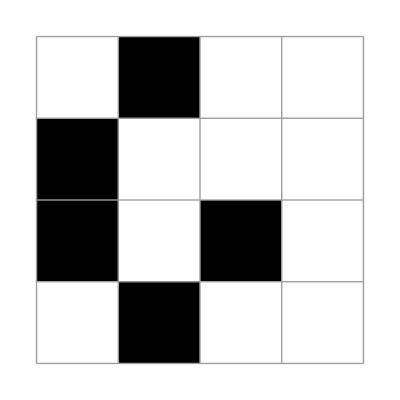
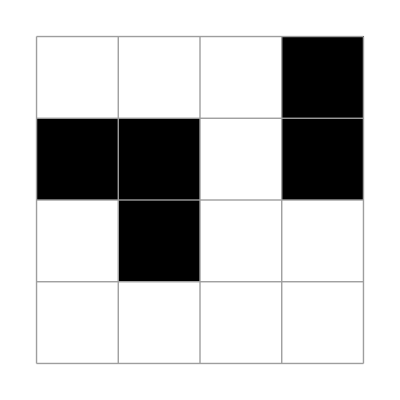
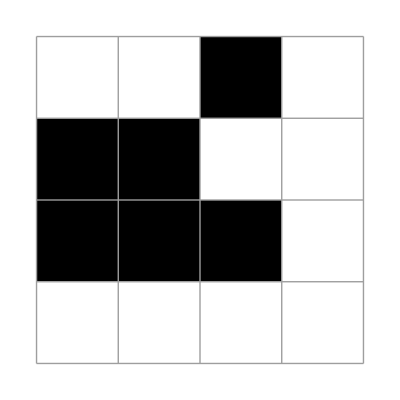
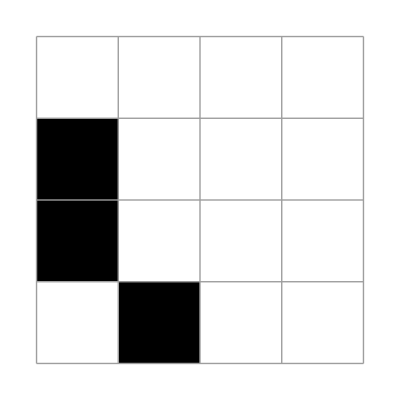
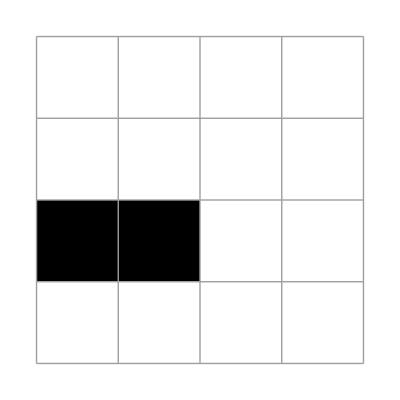
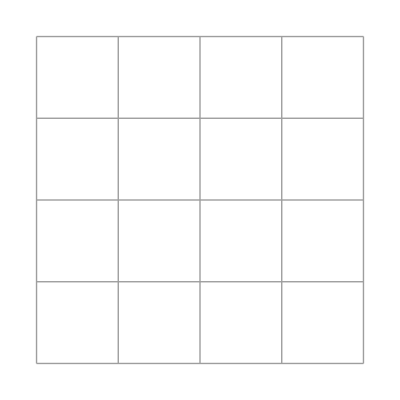
{0.815344,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

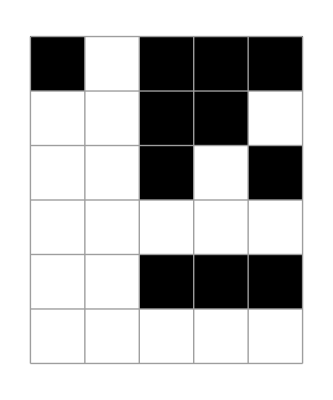

-Graphics-

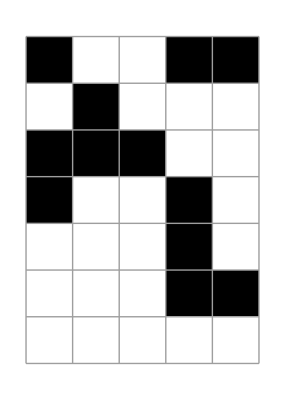

-Graphics-

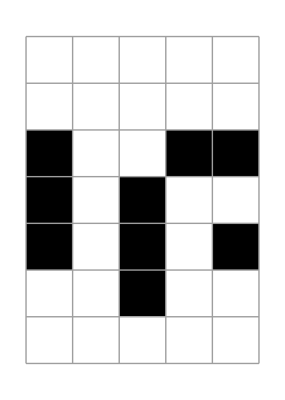

-Graphics-

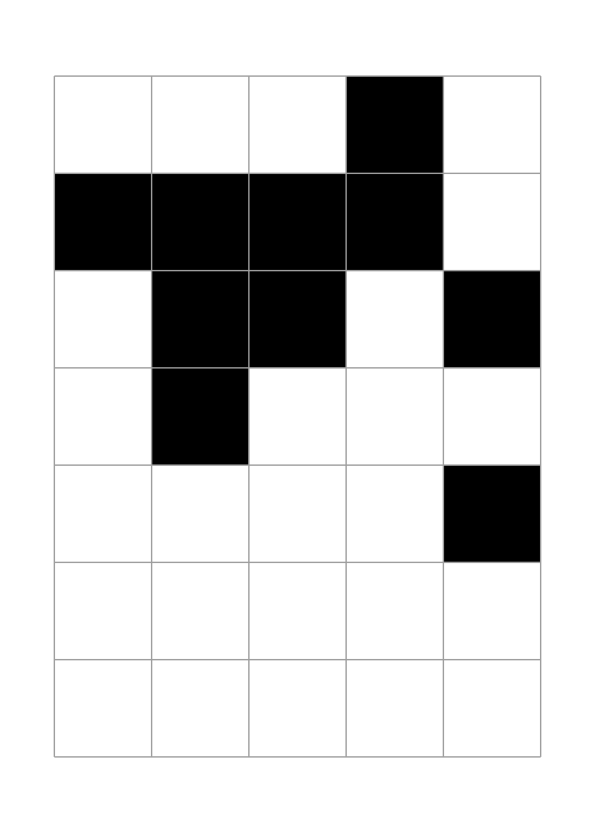

-Graphics-

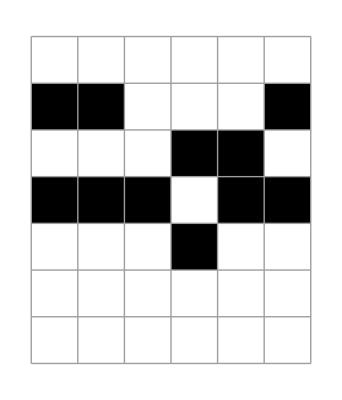

-Graphics-

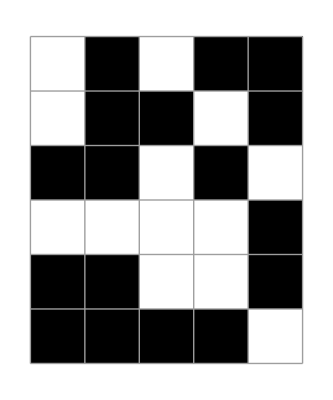

-Graphics-

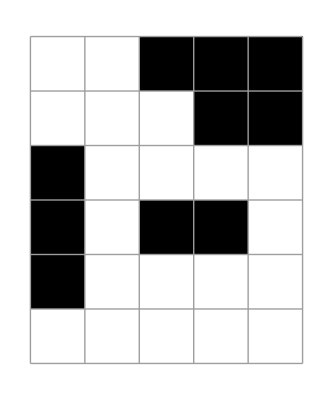

-Graphics-

```mathematica
seed=({{0, 1, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 0, 0, 0, 0, 1, 0, 1, 1}, {0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 0, 1}, {0, 1, 1, 1, 0, 1, 1, 0, 0, 1, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 1, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 1, 1, 0, 1, 0, 0, 0, 1, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1, 0}});
MessageDialog[ArrayPlot[seed,Mesh->True]];
ListAnimate[lifePlot[seed,3]]
```

ListAnimate[lifePlot[{{0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,1},{0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,1},{0,1,1,1,0,1,1,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,1,0},{0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0}},3]]

```mathematica
life44
```

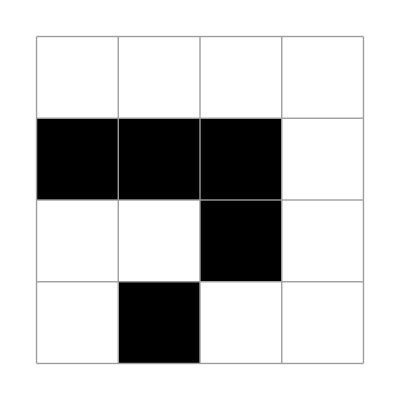
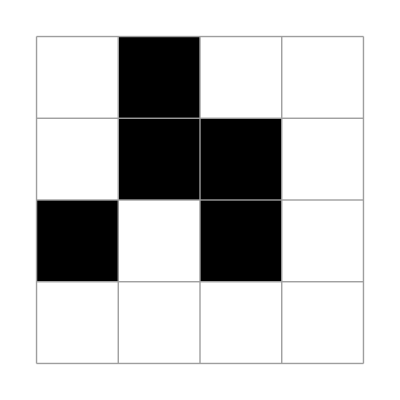
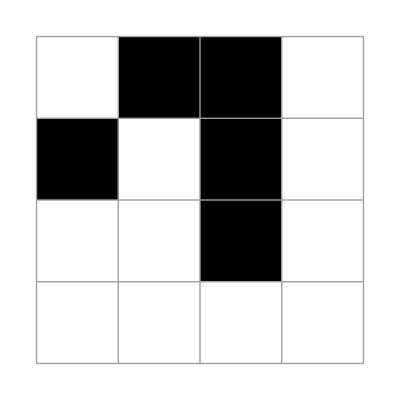
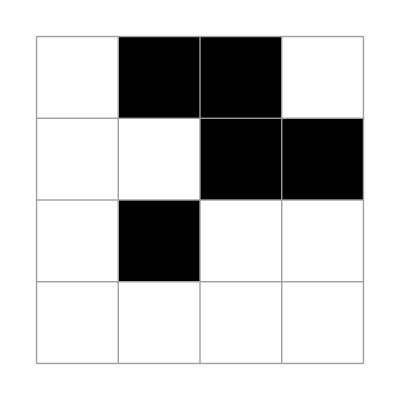

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife[{4,4}][ #]&,
X1,3]
```

```mathematica
lr
```

lifePlot::shdw: Symbol lifePlot appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

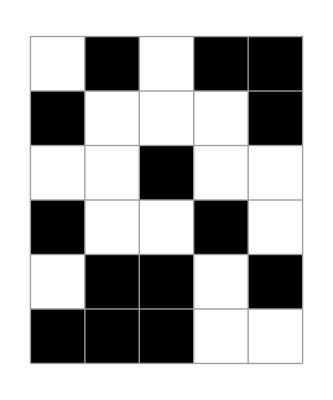
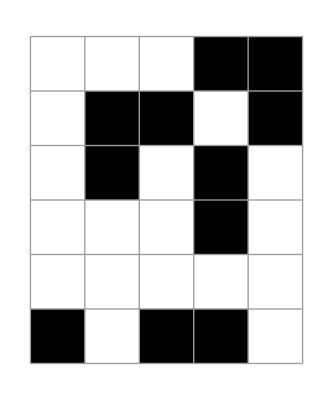
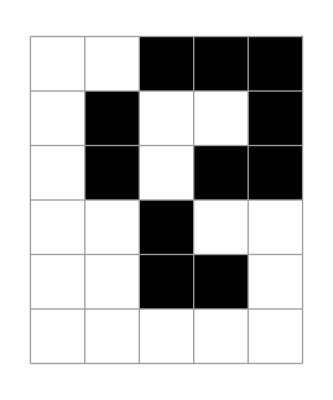
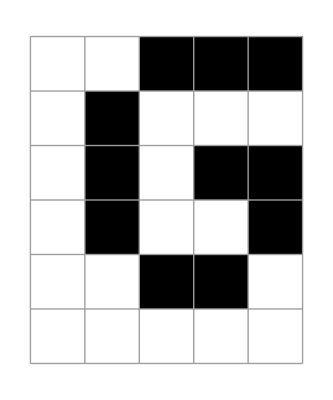

```mathematica
t65seed=({{0, 0, 1, 1, 1}, {0, 0, 0, 1, 1}, {1, 0, 0, 0, 0}, {1, 0, 1, 1, 0}, {1, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});z65seed=({{0, 1, 0, 1, 1}, {0, 1, 1, 0, 1}, {1, 1, 0, 1, 0}, {0, 0, 0, 0, 1}, {1, 1, 0, 0, 1}, {1, 1, 1, 1, 0}});
o65seed=({{1, 1, 0, 1, 1}, {1, 0, 1, 0, 1}, {1, 0, 0, 0, 0}, {1, 1, 1, 0, 1}, {1, 1, 0, 1, 1}, {0, 1, 0, 1, 1}});
g65seed=({{0, 1, 0, 1, 1}, {1, 0, 0, 0, 1}, {0, 0, 1, 0, 0}, {1, 0, 0, 1, 0}, {0, 1, 1, 0, 1}, {1, 1, 1, 0, 0}});
t65=NestList[updateLife[ #]&,
t65seed,3];
z65=NestList[updateLife[ #]&,
z65seed,3];
o65=NestList[updateLife[ #]&,
o65seed,3];
g65=NestList[updateLife[ #]&,
g65seed,3];
plt/@g65
```

```mathematica
copyNoteBookFileName
```

```mathematica
lr
```

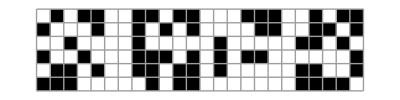
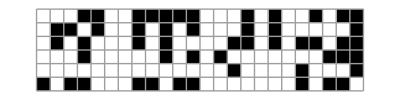
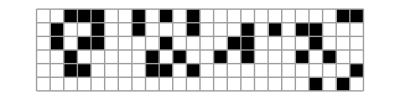
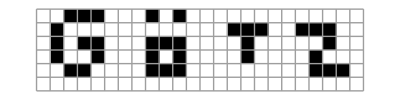
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
spacer=({{0}, {0}, {0}, {0}, {0}, {0}});frames=plt@Join[g65[[#]],spacer,spacer,o65[[#]],spacer,t65[[#]],spacer,z65[[#]],2]&/@Join[{1,2,3,4,1,2,3,4,4,4}
,{1,2,3,4,1,2,3,4,4,4}
,{1,2,3,4,1,2,3,4,4,4}
,{1,2,3,4,1,2,3,4,4,4}]
```

```mathematica
Export["~/Desktop/gotz1.gif",frames,"DisplayDurations"->Join[
{.1,.1,.1,.1,1,2,3,4,4,4}
,{.1,.1,.1,.1,1,2,3,4,4,4}
,{.1,.1,.1,.1,1,2,3,4,4,4}
,{.1,.1,.1,.1,1,2,3,4,4,4}]]
```

~/Desktop/gotz1.gif

```mathematica
frames=Rasterize[plt[#],RasterSize->200]&@Join[g65[[#]],spacer,spacer,spacer,o65[[#]],spacer,spacer,spacer,t65[[#]],spacer,spacer,spacer,z65[[#]],2]&/@Join[{1,2,3,4,1,2,3,4,4,4}
,{1,2,3,4,1,2,3,4,4,4}
,{1,2,3,4,1,2,3,4,4,4}
,{1,2,3,4,1,2,3,4,4,4}];
Export["~/Desktop/gotz3.gif",frames,"DisplayDurations"->Join[
{.1,.1,.1,.1,1,2,3,4,4,4}
,{.1,.1,.1,.1,1,2,3,4,4,4}
,{.1,.1,.1,.1,1,2,3,4,4,4}
,{.1,.1,.1,.1,1,2,3,4,4,4}]]
```

~/Desktop/gotz3.gif

```mathematica
Export["~/Desktop/gotz1.gif",.10frames,"DisplayDurations"->{.1,.1,.1,.1,1,2,3,4,4,4}];
```

Export::erropts: The value {0.1,0.1,0.1,0.1,1,2,3,4,4,4} specified for the option DisplayDurations is invalid.

safari ~/Desktop/gotz1.gif

## o

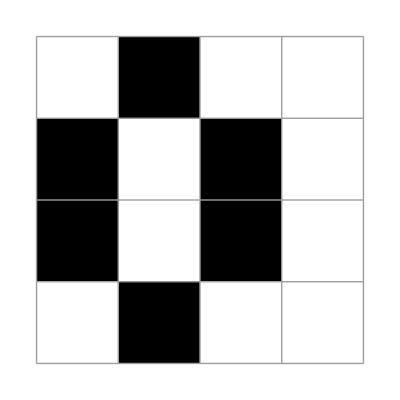
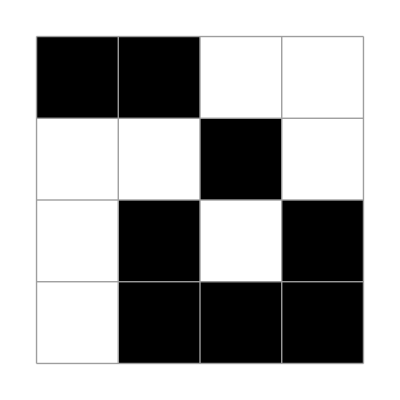
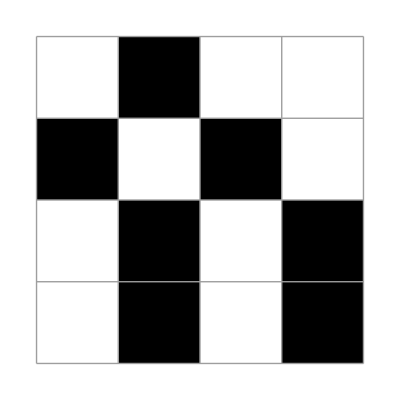
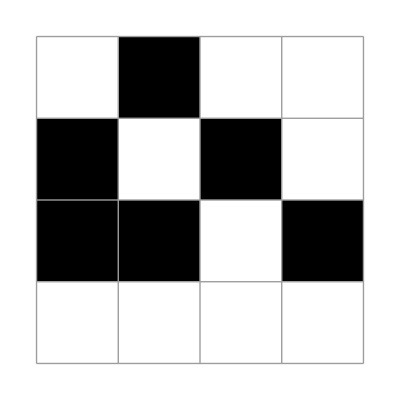
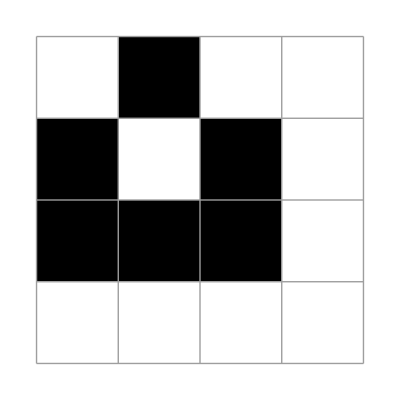
{0.944615,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

-Graphics-

```mathematica
({{□, □, □, □, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, □, □, 0, 0, 0, 1, 1, 0, 1, 0, 0, 0, 1, 1, 1, 0, 0}, {0, 0, 1, □, 0, 0, 0, 1, 0, 1, 1, 0, 0, 0, 0, 0, 1, 0, 0}, {1, 1, □, 1, 0, 0, 0, 1, 1, 1, 1, 0, 0, 0, 0, 1, 0, 0, 0}, {□, □, □, □, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 0}, {□, □, □, □, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})
```

{{□,□,□,□,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,□,□,0,0,0,1,1,0,1,0,0,0,1,1,1,0,0},{0,0,1,□,0,0,0,1,0,1,1,0,0,0,0,0,1,0,0},{1,1,□,1,0,0,0,1,1,1,1,0,0,0,0,1,0,0,0},{□,□,□,□,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0},{□,□,□,□,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## t

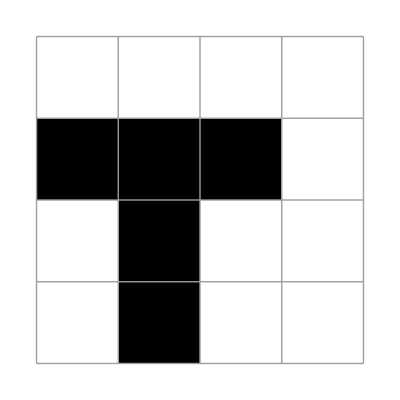
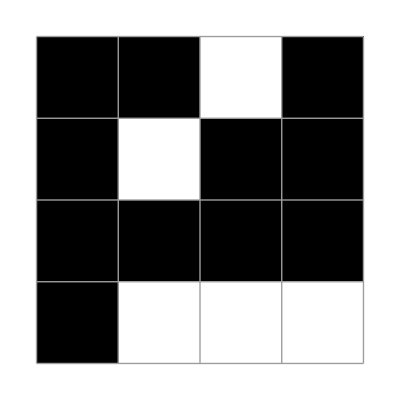
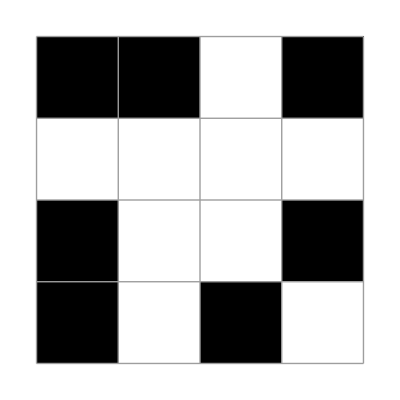
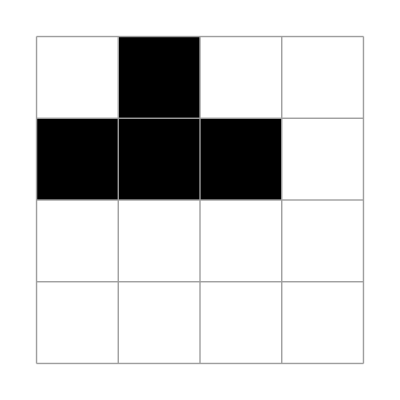
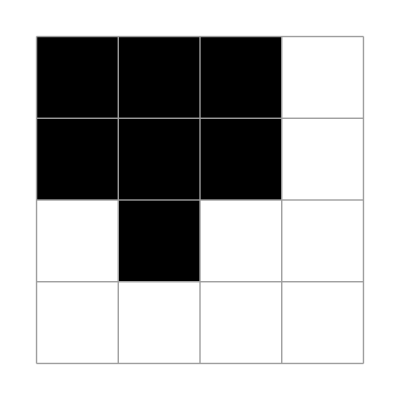
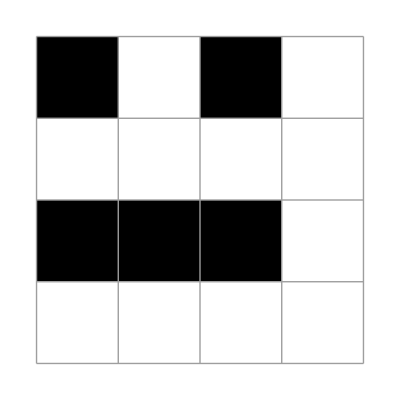
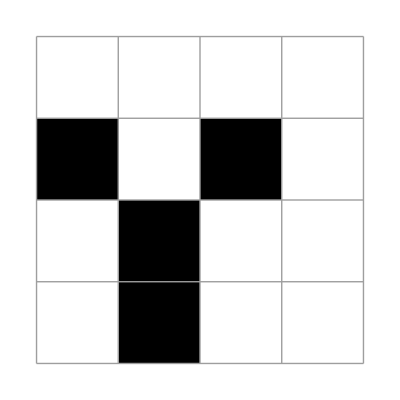
{0.821533,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 1, 0, 1, 0, 0, 0, 1, 1, 1, 0, 0}, {0, 0, 0, 1, 0, 1, 1, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1, 1, 1, 1, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,0,0,0,1,1,1,0,0},{0,0,0,1,0,1,1,0,0,0,0,0,1,0,0},{0,0,0,1,1,1,1,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## z

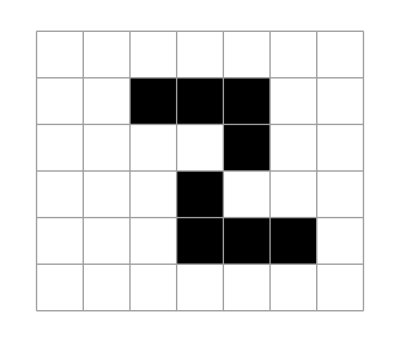

```mathematica
({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0}})//plt
```

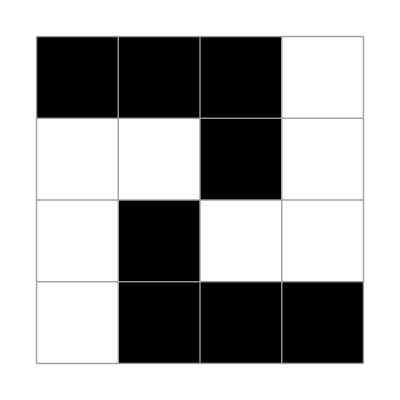

```mathematica
({{1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 1, 1, 1}})//plt
```

```mathematica
NestWhileList
```

NestWhileList

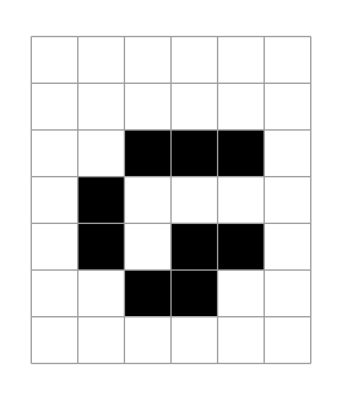
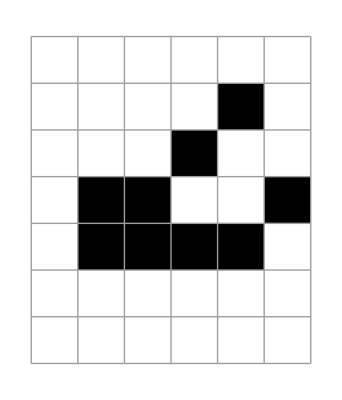
{119.767,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/00_still_life_stack_question/001_counting_function/countModule3.m"];
LIFE=({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 1, 0}, {0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0}, {0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 0, 0}});
MessageDialog[plt[LIFE]];
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPArray]*)
AbsoluteTiming[{LIFE//plt,rollBackPlot[LIFE,2]}]
```

```mathematica
Clear[x,i,j];Evaluate[BooleanCountingFunction[{0,5},Array[x,{3,3}]]]
```

True

```mathematica
form[xpArray_]:=Module[{formulaIJ,formula,varlist,out1,asdf,xp,i,j},{i,j}=Dimensions[xpArray];
x[_,0]=False;
x[0,_]=False;
x[_,j+1]=False;
x[i+1,_]=False;
Evaluate[Array[xp,{i,j}]]=loob[xpArray];
(**)(*({*)(*{xp[1,1],xp[1,2],xp[1,3],xp[1,4],xp[1,5]},*)(*{xp[2,1],xp[2,2],xp[2,3],xp[2,4],xp[2,5]},*)(*{xp[3,1],xp[3,2],xp[3,3],xp[3,4],xp[3,5]},*)(*{xp[4,1],xp[4,2],xp[4,3],xp[4,4],xp[4,5]},*)(*{xp[5,1],xp[5,2],xp[5,3],xp[5,4],xp[5,5]}*)(*})=loob[xpArray];*)formulaIJ=(and@{Nothing,(x[##]&&count[{0},{##}])~Implies~!xp[##],(x[##]&&count[{1},{##}])~Implies~!xp[##],(x[##]&&count[{2},{##}])~Implies~xp[##],(x[##]&&count[{3},{##}])~Implies~xp[##],(x[##]&&count[{4},{##}])~Implies~!xp[##],(x[##]&&count[{5},{##}])~Implies~!xp[##],(x[##]&&count[{6},{##}])~Implies~!xp[##],(x[##]&&count[{7},{##}])~Implies~!xp[##],(x[##]&&count[{8},{##}])~Implies~!xp[##]
(*not*),(!x[##]&&count[{0},{##}])~Implies~!xp[##],(!x[##]&&count[{1},{##}])~Implies~!xp[##],(!x[##]&&count[{2},{##}])~Implies~!xp[##],(!x[##]&&count[{3},{##}])~Implies~xp[##],(!x[##]&&count[{4},{##}])~Implies~!xp[##],(!x[##]&&count[{5},{##}])~Implies~!xp[##],(!x[##]&&count[{6},{##}])~Implies~!xp[##],(!x[##]&&count[{7},{##}])~Implies~!xp[##],(!x[##]&&count[{8},{##}])~Implies~!xp[##]})&;
formula=BooleanConvert[and@Flatten@Array[formulaIJ,{i,j}],"CNF"]];
f=form[({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}})];
f
```

(x[2,3]||!count[{2},{2,3}])&&(!x[1,1]||!count[{2},{1,1}])&&(!x[1,2]||!count[{2},{1,2}])&&(!x[1,3]||!count[{2},{1,3}])&&(!x[2,1]||!count[{2},{2,1}])&&(!x[2,2]||!count[{2},{2,2}])&&(!x[3,1]||!count[{2},{3,1}])&&(!x[3,2]||!count[{2},{3,2}])&&(!x[3,3]||!count[{2},{3,3}])&&!count[{3},{1,1}]&&!count[{3},{1,2}]&&!count[{3},{1,3}]&&!count[{3},{2,1}]&&!count[{3},{2,2}]&&!count[{0},{2,3}]&&!count[{1},{2,3}]&&!count[{4},{2,3}]&&!count[{5},{2,3}]&&!count[{6},{2,3}]&&!count[{7},{2,3}]&&!count[{8},{2,3}]&&!count[{3},{3,1}]&&!count[{3},{3,2}]&&!count[{3},{3,3}]

```mathematica
Expectation[x,x\[Distributed]ProbabilityDistribution[n x^(n-1)/θ^n,{x,0,θ}]]
```

(n θ)/(1+n)